# Псевдослучайные числа

```mathematica
Image@Partition[RandomReal[1,10000],100]
```

-Graphics-

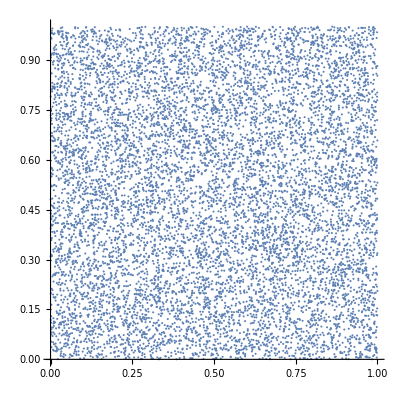

```mathematica
randoms=RandomReal[1,10000];
ListPlot[{randoms⟦;;-2⟧,randoms⟦2;;⟧}ᵀ,AspectRatio->1]
```

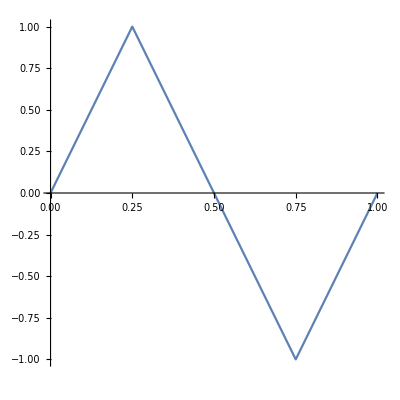

```mathematica
Plot[TriangleWave[x],{x,0,1},AspectRatio->1]
```

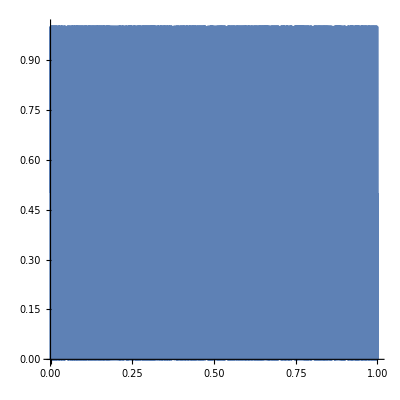

```mathematica
Plot[.5+.5TriangleWave[1000x],{x,0,1},MaxRecursion->15,AspectRatio->1]
```

```mathematica
rnd[x_]:=.5+.5TriangleWave[1234x];
```

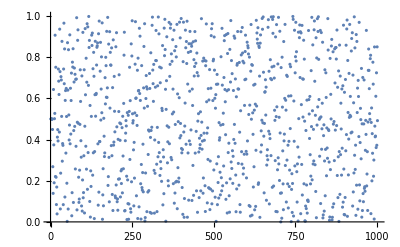

```mathematica
ListPlot@NestList[rnd,.5,1000]
```

```mathematica
Image@Partition[NestList[rnd,.5,10000],100]
```

-Graphics-

```mathematica
SeedRandom[2]
Image@Partition[RandomReal[1,10000],100]
```

-Graphics-

# Свертка изображений

```mathematica
img=-Graphics-;
```

```mathematica
ImageConvolve[img,1/11({{1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}})]
```

-Graphics-

```mathematica
kernel=1/11({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
ImageConvolve[img,kernel]
```

-Graphics-

```mathematica
kernel//Image
```

```mathematica
10-Graphics-
```

-Graphics-

```mathematica
kernel2=-Graphics-;
ImageConvolve[img,kernel2]
```

-Graphics-

```mathematica
DiskMatrix[10]
```

```mathematica
Image@DiskMatrix[10]
```

-Graphics-

```mathematica
kernel3=(1.#)/(Total@Total@#)&@DiskMatrix[10];
```

```mathematica
ImageConvolve[img,kernel3]
```

-Graphics-

```mathematica
kernel4=GaussianMatrix[10];
```

```mathematica
Image[kernel4]
```

```mathematica
200-Graphics-
```

-Graphics-

```mathematica
ImageConvolve[img,kernel4]
```

-Graphics-

# Приложения

свечение

детекция краев

```mathematica
ImageConvolve[img,({{-1, 1}})]
```

-Graphics-

```mathematica
-ImageConvolve[img,({{-1, 1}})]
Abs@ImageConvolve[img,({{-1, 1}})]
```

```mathematica
Abs@ImageConvolve[img,({{0, -1, 0}, {-1, 0, 1}, {0, 1, 0}})]
```

-Graphics-

частотное разложение

```mathematica
-Graphics--Graphics-
```

повышение резкости

# Деконволюция

```mathematica
blurred=ImageConvolve[img,GaussianMatrix[5]]
```

-Graphics-

```mathematica
ImageDeconvolve[blurred,GaussianMatrix[5]]
```

-Graphics-

```mathematica
img2=-Graphics-;
blurred2=ImageConvolve[img2,GaussianMatrix[6]]
```

-Graphics-

```mathematica
ImageDeconvolve[blurred2,GaussianMatrix[6]]
```

-Graphics-

```mathematica
noise=Image@RandomReal[.1,#]&@Reverse@ImageDimensions[blurred]
```

-Graphics-

```mathematica
blurred
blurred+noise
```

-Graphics-

-Graphics-

```mathematica
ImageDeconvolve[blurred+noise,GaussianMatrix[5]]
```

-Graphics-